Load the package:

```mathematica
<<PatrickMLenggenhager`HyperBloch`
```

Open the documentation:

```mathematica
Documentation`HelpLookup["PatrickMLenggenhager/HyperBloch/tutorial/BasicUsage"];
```

```mathematica
Documentation`HelpLookup["PatrickMLenggenhager/HyperBloch/guide/HyperBlochPackage"];
```

Load the previously exported HyperCells data from the current directory:

```mathematica
SetDirectory[NotebookDirectory[]];

pcell=ImportCellGraphString[Import["(2,8,8)_T2.6_3.hcc"]];
pcmodel=ImportModelGraphString[Import["{8,8}-tess_T2.6_3.hcm"]];
scmodel=ImportSupercellModelGraphString[Import["{8,8}-tess_T2.6_3_sc-T3.11.hcs"]];
```

Visualize the model on the primitive cell:

```mathematica
VisualizeModelGraph[pcmodel,Elements-><|ShowCellGraphFlattened->{},ShowCellBoundary->{ShowEdgeIdentification->True}|>,CellGraph->pcell,NumberOfGenerations->2,ImageSize->300]
```

-Graphics-

Construct the Abelian Bloch Hamiltonian:

```mathematica
FullSimplify[AbelianBlochHamiltonianExpression[pcmodel,1,0&,-1&,k]]
```

{{-2 (Cos[k[1]]+Cos[k[2]]+Cos[k[3]]+Cos[k[4]])}}

Compile it for more efficient evaluation:

```mathematica
Hpc=AbelianBlochHamiltonian[pcmodel,1,0&,-1&,CompileFunction->True];
```

Compute the density of states:

```mathematica
ComputeDOS[cfH_,Npts_,Nruns_,{Emin_,Emax_},dE_]:=Module[{data,tot,dimk=Length[cfH[[2]]]},data=Transpose[{MovingAverage[Range[Emin,Emax,dE],2],Total@ParallelTable[HistogramList[Flatten@Table[Chop@Eigenvalues[cfH@@RandomReal[{-Pi,Pi},dimk]],{i,1,Round[Npts/Nruns]}],{Emin,Emax,dE}][[2]],{j,1,Nruns},Method->"FinestGrained"]}];
tot=Total@data[[;;,2]];
{#1,#2/dE/tot}&@@@data]
dospc=ComputeDOS[Hpc,10^6,32,{-8-0.005,8},0.005];
```

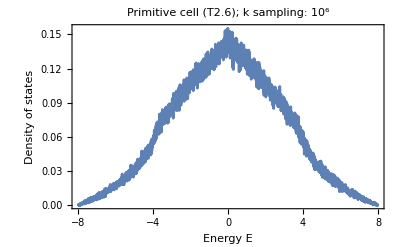

```mathematica
ListLinePlot[dospc,Frame->True,FrameStyle->Black,FrameLabel->{"Energy E","Density of states"},PlotRange->All,PlotLabel->"Primitive cell (T2.6); k sampling: 10^6"]
```

Compute the density of states on the supercell:

```mathematica
Hsc=AbelianBlochHamiltonian[scmodel,1,0&,-1&,PCModel->pcmodel,CompileFunction->True];
dossc=ComputeDOS[Hsc,10^4,32,{-8-0.005,8},0.005];
```

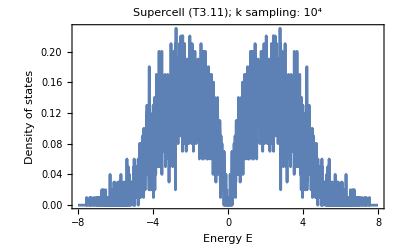

```mathematica
ListLinePlot[dossc,Frame->True,FrameStyle->Black,FrameLabel->{"Energy E","Density of states"},PlotRange->All,PlotLabel->"Supercell (T3.11); k sampling: 10^4"]
```